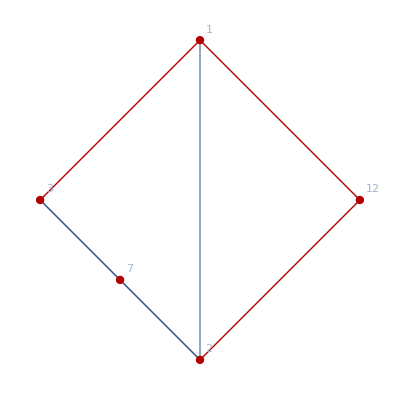
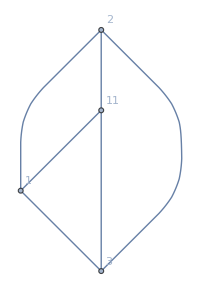
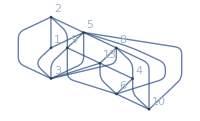
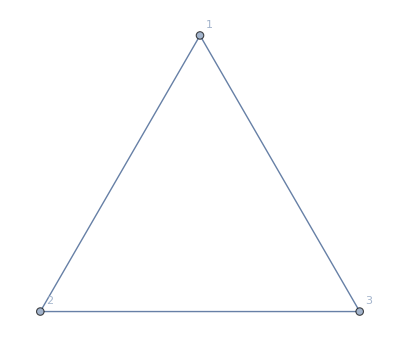
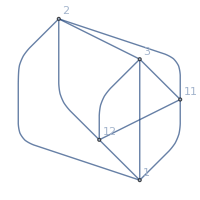
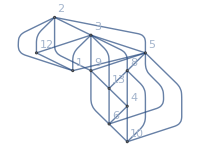
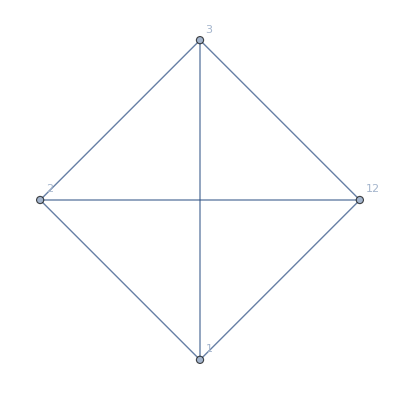
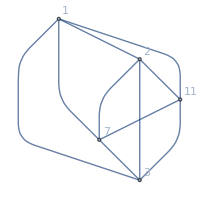
{10087,v,-Graphics-}→{{{{1,7},{2},{3,12}},-Graphics-{(-3+x) (-2+x),24},-Graphics-{(-3+x)^3 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72},-Graphics-{-2+x,24},(-3+x) (-2+x) (-1+x) x,(-3+x)^3 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-2+x) (-1+x) x,{v1x2x3xb},{v189x2adx36x45,v19ax268x34x5d,v149x268x3ax5d},{v1x2x3}},{{{1,7},{2},{3},{12}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-3+x) (-2+x) (-1+x) x,{},{v189x2adx36x45c,v149x268x3ax5cd,v19ax268x34x5cd},{v1x2x3xc}},{{{1},{2},{3,12},{7}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-3+x) (-2+x) (-1+x) x,{},{v145x2adx36x789,v15dx268x3ax479,v15dx268x34x79a},{v1x2x3x7}},{{{1},{2},{3},{7,12}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-3+x) (-2+x) (-1+x) x,{},{v145x2adx36x789,v15dx268x3ax479,v15dx268x34x79a},{v1x2x3x7}},{{{1},{2},{3},{7},{12}},-Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0},-Graphics-{(-4+x) (-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),0},-Graphics-{(-4+x) (-3+x) (-2+x),0},(-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x,(-4+x) (-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-4+x) (-3+x) (-2+x) (-1+x) x,{},{},{}}}{(-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),{1,2,3,12,7},5,{v1789x2adx36cx45b,v179ax268x34cx5bd,v1479x268x3acx5bd}}

```mathematica
With[{k=10087},
Block[{g=ReadGrof[k],vertices, adj},
vertices={1,2,3,12,7};
adj={1,2,3,12,7};
{Style[k,If[OddQ[k],Blue,Purple]],v,Subgraph[Graph[g,GraphHighlight->Join[adj,CollectMPGEdges[g]],VertexLabels->"Name",GraphLayout->"PlanarEmbedding",VertexStyle->{v->Green},VertexSize->{v->Large}],Append[adj,v],GraphLayout->"TutteEmbedding"]}->Labeled[ZykovDecomposition23[g,vertices],Style[{Factor[ChromaticPolynomial[g,x]],adj,ZykovSolutionCount[g,adj],FindFullFormula1234[g]},Bold,24]]
]
]
```